```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week9

```mathematica
data=ReadList["!./metropolis 100000",Number];
```

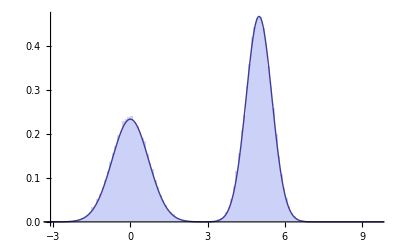

```mathematica
Show[Histogram[data[[;;;;100]],100,"PDF"],Plot[p[x]/n,{x,-5,15},PlotRange->All]]
```

```mathematica
p[x_]:=Exp[-x^2]+2Exp[-(x-5)^2/.5];
n=NIntegrate[p[x],{x,-Infinity,Infinity}];
```

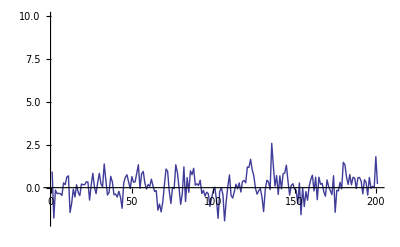

```mathematica
ListLinePlot[data[[100;;4100;;20]],PlotRange->{-2,10}]
```

```mathematica
dataind=RandomVariate[NormalDistribution[0,1/√2],200];
```

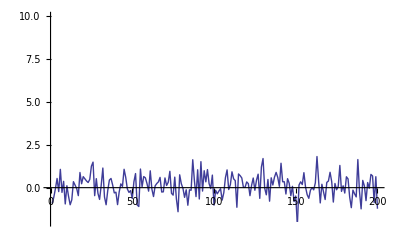

```mathematica
ListLinePlot[dataind,PlotRange->{-2,10}]
```

#### Metropolis simulations for 2 dim particle gas

```mathematica
data=Partition[ReadList["!./gas 10 10 1 1 1 10000 10",Number],41];
```

```mathematica
data[[10]]
```

{9,0.569369,0.298397,1.10843,-0.305874,5.22261,1.11468,0.104846,-0.498696,1.54611,2.98147,0.195827,-0.850292,4.2615,7.06639,0.525644,-0.149831,1.19109,1.20215,0.673803,-1.80414,0.629395,5.7907,-0.840478,-0.909298,1.41507,4.59576,-0.919319,0.34463,0.914003,8.04592,1.88124,0.520215,6.72207,1.4366,-0.35976,-1.13795,3.24078,6.75491,-0.79548,-0.544443}

```mathematica
display[l_,n_,sz_]:=Graphics[{{FaceForm[],EdgeForm[Black],Rectangle[{0,0},{sz,sz}]},AbsolutePointSize[6],Table[Point[{l[[2+4*i]],l[[3+4*i]]}],{i,0,n-1}]},PlotRange->{{-0.2,sz+0.2},{-0.2,sz+0.2}}]
```

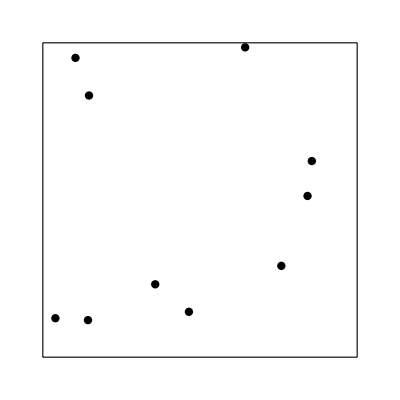

```mathematica
display[data[[200]],10,10]
```

```mathematica
lj[r1_,r2_]:=Module[{r=Norm[r1-r2]},4 (1/r^12-1/r^6)]
pot[l_,n_]:=Sum[lj[{l[[2+4*i]],l[[3+4*i]]},{l[[2+4*j]],l[[3+4*j]]}],{i,0,n-1},{j,i+1,n-1}]
```

```mathematica
ken[l_,n_]:=0.5 Sum[l[[4+4*i]]^2+l[[5+4*i]]^2,{i,0,n-1}]
```

```mathematica
kenlist=Table[ken[d,10],{d,data}];
```

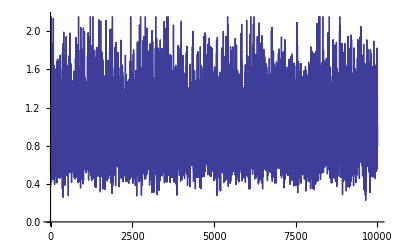

```mathematica
ListLinePlot[kenlist/10]
```

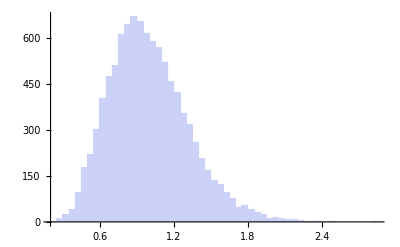

```mathematica
Histogram[kenlist/10]
```

```mathematica
Mean[kenlist/10]
```

0.997202

#### Extra stuff (how about computing the pressure?)

Ideal gas equation of state is p/kT = n.
For a gas that is not ideal the equation of state changes. Mayer cluster expansion allows us to compute the virial expansion; for kT = 1 for this gas we have
p/kT = n - 1.07347 n^2 + 2.427 n^3 + 0.25 n^4 + ...
Can we check this with our code?

One cool bit of physics is that the pressure changes from the ideal case because the density of particles around the walls is reduced. To see this, we plot the histogram for the x poistions of the particle in our simulations.

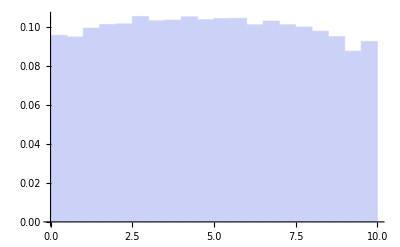

```mathematica
(* the PDF of positions corresponds to the probability density of finiding a particle around position x. For uniform distribution we expect N/L = 10 particles / 10 distance units = 0.1.

Note that away form the walls we have the expected density, but not close to the walls *)
Histogram[Flatten[data[[;;,2;;;;4]]],20,"PDF",GridLines->{{},{10/100}}]
```

The pressure can be computed from the density close to the walls : we have p/kT = n, where n is the density close to the walls. We compute the number of particles a distance dx from the walls divided by the area corresponding to this region. The density should not depend on dx too much and we want to compute it in the limit that dx goes to zero. However, we cannot take dx too small since then error on this quantity will be small. The following function computes this average :

```mathematica
densityatwall[cfg_,l_,dx_]:=Module[{xs=cfg[[2;;;;4]],ys=cfg[[3;;;;4]],p,nclosetowall,area},
p=Transpose[{xs,ys}];
nclosetowall=Length[Select[p,Abs[#[[1]]-l/2]>l/2-dx||Abs[#[[2]]-l/2]>l/2-dx&]];
area=4*dx(l-dx);
nclosetowall/area]
```

```mathematica
denslist=Table[densityatwall[d,10,.5],{d,data[[1000;;]]}];
```

```mathematica
(* Compute mean and error of list *)
meaner[l_]:={Mean[l],StandardDeviation[l]/Sqrt[Length[l]]}
```

```mathematica
meaner[denslist]
```

{0.09489,0.000664481}

```mathematica
(* recompute the denslist but with dx=0.25 rather than 0.5 as above *)
denslist=Table[densityatwall[d,10,.25],{d,data[[1000;;]]}];
pres=meaner[denslist]
```

{0.0962058,0.000993649}

Note that the results above for dx = 0.25  are similar to dx = 0.5 but the error increased.

The pressure is then p/kT = {0.0962, 0.00099} 
for density n = 10/10^2 = 0.1. Lets compare to virial expansion.The dotted line is the ideal gas and the solid one is the virial.

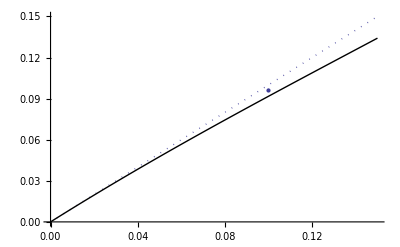

```mathematica
Needs["ErrorBarPlots`"]
Show[Plot[{n,n-1.07347 n^2+2.427 n^3+0.25 n^4},{n,0.0,.15},PlotStyle->{Dotted,Black}],ErrorListPlot[{{0.1,pres[[1]],pres[[2]]}}]]
```

#### Lets repeat this for 25 particles in the box

```mathematica
data=Partition[ReadList["!./gas 25 10 1 1 1 10000 10",Number],101];
```

```mathematica
denslist=Table[densityatwall[d,10,.25],{d,data[[1000;;]]}];
pres=meaner[denslist]
```

{0.229752,0.00150851}

The pressure is then p/kT = {0.230, 0.001} 
for density n = 25/10^2 = 0.25. Lets compare to virial expansion. The dotted line is the ideal gas and the solid one is the virial.

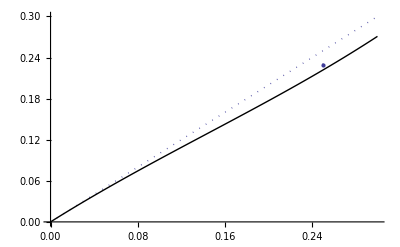

```mathematica
Needs["ErrorBarPlots`"]
Show[Plot[{n,n-1.07347 n^2+2.427 n^3+0.25 n^4},{n,0.0,.3},PlotStyle->{Dotted,Black}],ErrorListPlot[{{0.25,pres[[1]],pres[[2]]}}]]
```